```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

hmc::shdw: Symbol hmc appears in multiple contexts {Sampler1`,Global`}; definitions in context Sampler1` may shadow or be shadowed by other definitions.

HessianH::shdw: Symbol HessianH appears in multiple contexts {Sampler1`,Global`}; definitions in context Sampler1` may shadow or be shadowed by other definitions.

GradientG::shdw: Symbol GradientG appears in multiple contexts {Sampler1`,Global`}; definitions in context Sampler1` may shadow or be shadowed by other definitions.

PARTICLES::shdw: Symbol PARTICLES appears in multiple contexts {Sampler1`,Global`}; definitions in context Sampler1` may shadow or be shadowed by other definitions.

STEPS::shdw: Symbol STEPS appears in multiple contexts {Sampler1`,Global`}; definitions in context Sampler1` may shadow or be shadowed by other definitions.

AC::shdw: Symbol AC appears in multiple contexts {Sampler1`,Global`}; definitions in context Sampler1` may shadow or be shadowed by other definitions.

```mathematica
σ=0.00001;
```

```mathematica
SIGMA={{σ^2,0},{0,1}};
```

```mathematica
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
```

```mathematica
dU[x_,y_]=GradientG[U[x,y],{x,y}];
```

```mathematica
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.×10^10,0.},{0.,1.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

1001 -861221. 4.71522 0.0100763 0.0264781 861521. 300 300 4.08391×10^-8 4.0509×10^-6 True {1,3} {11}

2002 -43015.7 2.93794 0.990984 0.017315 43315.7 300 300 2.53309×10^-8 0.0000718502 False {1,11} {1,11}

3003 -1839.95 11.2675 0.93351 0.100054 2139.95 300 300 3.84723×10^-8 0.000839088 True {1,3,11} {1,11}

4004 317.465 5.21804 0.871053 0.172074 5.59782 308.297 323.063 1.3345×10^-7 0.00705637 False {1,3,5,11} {1,11}

5005 303.554 7.86874 0.568504 0.393413 10.7978 314.352 331.953 1.7809×10^-7 0.0114902 True {1,11} {1,11}

6006 326.261 6.67517 0.857842 0.170634 5.69205 314.352 331.953 1.7809×10^-7 0.0114902 False {1,4,5,11} {1,11}

7007 300.9 14.061 0.882336 0.287411 13.4515 314.352 331.953 1.7809×10^-7 0.0114902 True {1,7,8,11} {1,11}

8008 320.965 10.1287 0.779415 0.325893 10.9874 314.352 331.953 1.7809×10^-7 0.0114902 False {1,11} {1,11}

9009 300.688 15.7561 0.715664 0.415133 13.6642 314.352 331.953 1.7809×10^-7 0.0114902 True {1,2,5,7,10,11} {1,11}

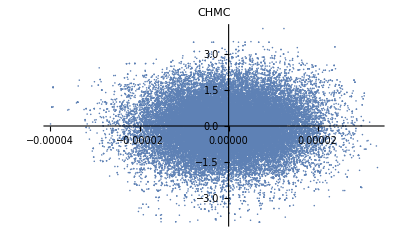

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True];
ListPlot[QS,PlotLabel->CHMC]
```

1001 -42642.5 8.79834 0.466544 0.417327 42942.5 300 300 2.43425×10^-8 1.×10^-7 True {1,3,6,11} {1,11}

2002 306.144 8.17924 0.806528 0.23908 6.01045 312.154 300 1.25716×10^-7 1.×10^-7 True {1,4,9,10,11} {1,11}

3003 307.748 4.01645 0.754528 0.316749 11.463 319.211 300 2.26127×10^-7 1.×10^-7 True {1,8,11} {1,11}

4004 314.109 11.6159 0.632301 0.242303 6.65546 320.765 300 2.47312×10^-7 1.×10^-7 True {1,3,4,11} {1,11}

5005 312.551 6.55623 0.54569 0.368554 9.46061 322.011 300 2.37662×10^-7 1.×10^-7 True {1,2,3,11} {1,11}

6006 313.147 16.7545 0.450056 0.386193 8.86454 322.011 300 2.37662×10^-7 1.×10^-7 True {1,11} {1,11}

7007 313.4 9.70419 0.637892 0.349768 8.6114 322.011 300 2.37662×10^-7 1.×10^-7 True {1,3,4,8,11} {1,11}

8008 309.663 7.56289 0.549837 0.373296 12.3486 322.011 300 2.37662×10^-7 1.×10^-7 True {1,6,10,11} {1,11}

9009 312.936 9.66757 0.587999 0.428784 9.07552 322.011 300 2.37662×10^-7 1.×10^-7 True {1,5,6,9,11} {1,11}

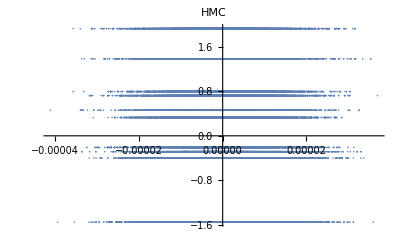

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False];
ListPlot[QS,PlotLabel->HMC]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.×10^10,0.},{0.,1.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

1001 -5.49481×10^10 3.3701 0.551597 0.402503 5.49481×10^10 300 300 1.×10^-7 1.14482×10^-6 False {1,11} {1,7,10,11}

2002 -5.49481×10^10 5.97014 0.714809 0.433782 5.49481×10^10 300 300 1.×10^-7 1.93986×10^-6 False {1,11} {1,8,11}

3003 -5.49481×10^10 4.59831 0.611514 0.477227 5.49481×10^10 300 300 1.×10^-7 2.7208×10^-6 False {1,5,11} {1,2,5,11}

4004 -5.4948×10^10 3.45387 0.507706 0.439644 5.4948×10^10 300 300 1.×10^-7 3.66722×10^-6 False {1,2,6,7,11} {1,6,7,10,11}

5005 -5.4948×10^10 2.83185 0.703275 0.477848 5.4948×10^10 300 300 1.×10^-7 4.6103×10^-6 False {1,2,4,7,11} {1,5,11}

6006 -5.49479×10^10 5.75978 0.40109 0.51547 5.49479×10^10 300 300 1.×10^-7 4.6103×10^-6 False {1,11} {1,3,11}

7007 -5.49478×10^10 8.00919 0.608157 0.505977 5.49478×10^10 300 300 1.×10^-7 4.6103×10^-6 False {1,3,5,9,10,11} {1,3,11}

8008 -5.49477×10^10 3.03637 0.715587 0.441848 5.49477×10^10 300 300 1.×10^-7 4.6103×10^-6 False {1,2,3,11} {1,2,11}

9009 -5.49476×10^10 3.82281 0.619831 0.493859 5.49476×10^10 300 300 1.×10^-7 4.6103×10^-6 False {1,2,11} {1,3,4,9,11}

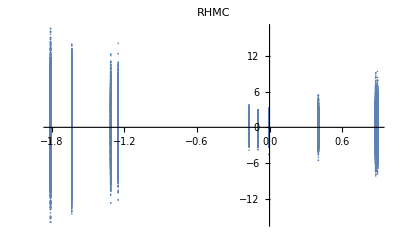

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,False,False];
ListPlot[QS,PlotLabel->RHMC]
```